```mathematica
H[kx_,ky_,b_,t2_]:=-({{-2.5, Exp[-I(1-b)kx]+t2 Exp[I(1+b)kx], Exp[-I(1-b)(kx/2+Sqrt[3]ky/2)]+t2 Exp[I(1+b)(kx/2+Sqrt[3]ky/2)]}, {Exp[I(1-b)kx]+t2 Exp[-I(1+b)kx], 0, Exp[-I(1-b)(-kx/2+Sqrt[3]ky/2)]+t2 Exp[I(1+b)(-kx/2+Sqrt[3]ky/2)]}, {Exp[I(1-b)(kx/2+Sqrt[3]ky/2)]+t2 Exp[-I(1+b)(kx/2+Sqrt[3]ky/2)], Exp[I(1-b)(-kx/2+Sqrt[3]ky/2)]+t2 Exp[-I(1+b)(-kx/2+Sqrt[3]ky/2)], 0}});
```

```mathematica
EE[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky,0.0,1]]];
```

```mathematica
Plot3D[EE[x,y],{x,-2Pi/3,2Pi/3},{y,-Pi/Sqrt[3],Pi/Sqrt[3]},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤2Pi/3&&Abs[x-y/Sqrt[3]]≤2Pi/3],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

-Graphics3D-

```mathematica
MatrixForm[Table[1,{i,3},{j,3}]]
```

```mathematica
HHH=-({{t, 1, 1}, {1, 0, 1}, {1, 1, 0}});
```

```mathematica
Eigensystem[HHH]
```

{{1,1/2 (-1-t-√(9-2 t+t^2)),1/2 (-1-t+√(9-2 t+t^2))},{{0,-1,1},{-1/2+t/2+1/2 √(9-2 t+t^2),1,1},{-1/2+t/2-1/2 √(9-2 t+t^2),1,1}}}

```mathematica
HHH1=-({{0, 1, 1}, {1, 0, -1}, {1, -1, 0}});
```

```mathematica
Eigensystem[HHH1]
```

{{2,-1,-1},{{-1,1,1},{1,0,1},{1,1,0}}}

```mathematica
H[kx_,ky_,b_,t2_,t3_]:=-({{0, (Exp[-I(1-b)kx]+t2 Exp[I(1+b)kx])t3, Exp[-I(1-b)(kx/2+Sqrt[3]ky/2)]+t2 Exp[I(1+b)(kx/2+Sqrt[3]ky/2)]}, {(Exp[I(1-b)kx]+t2 Exp[-I(1+b)kx])t3, 0, (Exp[-I(1-b)(-kx/2+Sqrt[3]ky/2)]+t2 Exp[I(1+b)(-kx/2+Sqrt[3]ky/2)])}, {Exp[I(1-b)(kx/2+Sqrt[3]ky/2)]+t2 Exp[-I(1+b)(kx/2+Sqrt[3]ky/2)], (Exp[I(1-b)(-kx/2+Sqrt[3]ky/2)]+t2 Exp[-I(1+b)(-kx/2+Sqrt[3]ky/2)]), 0}});
```

```mathematica
EE[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky,0.0,1,100]]];
```

```mathematica
Plot3D[EE[x,y],{x,-2Pi/3,2Pi/3},{y,-Pi/Sqrt[3],Pi/Sqrt[3]},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤2Pi/3&&Abs[x-y/Sqrt[3]]≤2Pi/3],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

-Graphics3D-

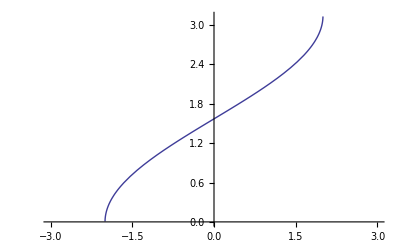

```mathematica
Plot[ArcCos[β Cos[2Pi/3]],{β,-3,3}]
```